```mathematica
subG = {gL-> s2W - 1/2,gR-> s2W};
subGVA = {gV-> 2s2W - 1/2,gA-> 1/2};
subGLRtoVA={gL -> (gV - gA)/2,gR->(gV + gA)/2 };
subS2W={s2W-> 0.2334, ds2W-> 0.0083};
```

```mathematica
g1=gL^2;
g2=gR^2;
g3=(gL+1)^2;

(*Processes:A_i values for different scattering processes*)
Aνμ={1,(1-y)^2,0}; (*νμ e->νμ e*)
Aν̄μ={(1-y)^2,1,0}; (*ν̄μ e->ν̄μ e*)
Aνe={0,(1-y)^2,1}; (*νe e->νe e*)
Aν̄e={0,1,(1-y)^2}; (*ν̄e e->ν̄e e*)

(*Differential Cross-Section Function*)
σ[A_]:=(2 GF^2 Me Enu/π) (A[[1]] g1+A[[2]] g2+A[[3]] g3);
σtot[A_]:=Integrate[σ[A],{y,0,1}];
(*Calculate Differential Cross-Sections for each process*)
σνμ=σ[Aνμ];
σν̄μ=σ[Aν̄μ];
σνe=σ[Aνe];
σν̄e=σ[Aν̄e];

σtotνμ=σtot[Aνμ]//FullSimplify
σtotν̄μ=σtot[Aν̄μ]//FullSimplify
σtotνe=σtot[Aνe]//FullSimplify
σtotν̄e=σtot[Aν̄e]//FullSimplify
```

(2 Enu GF^2 (3 gL^2+gR^2) Me)/(3 π)

```mathematica
n
```

(2 Enu GF^2 (gL^2+3 gR^2) Me)/(3 π)

(2 Enu GF^2 (3 (1+gL)^2+gR^2) Me)/(3 π)

(2 Enu GF^2 (1/3 (1+gL)^2+gR^2) Me)/π

-1+gA-gV

-((1+2 gL) (-1+y)^2)

(1+gL)^2+gR^2 (1-y)^2

gR^2+(1+gL)^2 (1-y)^2

```mathematica
σμplus = σν̄μ + σνe//Simplify;
σμminus = σνμ + σν̄e//Simplify;
σtotμplus = σtotν̄μ + σtotνe//Simplify;
σtotμminus = σtotνμ + σtotν̄e//Simplify;

σμplusFlavored = (σν̄μ/.{gL-> gLµ, gR-> gRµ}) + (σνe/.{gL-> gLe, gR-> gRe})//Simplify;
σμminusFlavored = (σνμ/.{gL-> gLµ, gR-> gRµ}) + (σν̄e/.{gL-> gLe, gR-> gRe})//Simplify;
σtotμplusFlavored = (σtotν̄μ/.{gL-> gLµ, gR-> gRµ}) + (σtotνe/.{gL-> gLe, gR-> gRe})//Simplify;
σtotμminusFlavored = (σtotνμ/.{gL-> gLµ, gR-> gRµ}) + (σtotν̄e/.{gL-> gLe, gR-> gRe})//Simplify;
```

```mathematica
Rdiff=(σμplus - σμminus)/(σtotμplus + σtotμminus)/.subG//FullSimplify
Rdifffdiff=(σμplus - σμminus)/(σμplus + σμminus)/.subG//FullSimplify
Rtot=(σtotμplus - σtotμminus)/(σtotμplus + σtotμminus)/.subG//FullSimplify
Rtotfluxcorrected=(σtotν̄μ + r σtotνe -  (σtotνμ + r σtotν̄e))/(σtotν̄μ + r σtotνe +  (σtotνμ + r σtotν̄e))/.subG//FullSimplify
```

-(3 s2W (-2+y) y)/(1+8 s2W^2)

-(4 s2W (-2+y) y)/((1+8 s2W^2) (2+(-2+y) y))

(2 s2W)/(1+8 s2W^2)

(-1+r+4 (1+r) s2W)/(2 (1+r+4 (-1+r) s2W+8 (1+r) s2W^2))

```mathematica
Series[Rtotfluxcorrected/.r-> 1+eps,{eps,0,1}]//Simplify
```

(2 s2W)/(1+8 s2W^2)+((1-8 s2W^2) eps)/(4 (1+8 s2W^2)^2)+O[eps]^2

```mathematica
(σμplus - σμminus)/(σtotμplus + σtotμminus)//FullSimplify
(σtotμplus - σtotμminus)/(σtotμplus + σtotμminus)/.subGLRtoVA//FullSimplify
```

-(3 (1+2 gL) (-2+y) y)/(4+8 gL (1+gL)+8 gR^2)

(1-gA+gV)/(2 (1+(-1+gA) gA+gV+gV^2))

```mathematica
(σtotν̄μ -σtotνμ)/(σtotν̄μ +σtotνμ)/.subGLRtoVA//Simplify
(σtotνe-σtotν̄e)/(σtotνe+σtotν̄e)/.subGLRtoVA//Expand//Simplify
(σtotν̄μ +σtotνe)/(σtotνμ +σtotν̄e)//Simplify
(σtotνe-σtotν̄e)/(σtotνe+σtotν̄e)/.subGLRtoVA//Expand//Simplify

 σtotν̄μ -σtotνμ//Simplify
σtotνe-σtotν̄e//Expand//Simplify
σtotν̄μ -σtotνμ +σtotνe-σtotν̄e//Simplify
```

(gA gV)/(gA^2+gV^2)

-((-1+gA) (1+gV))/(2-2 gA+gA^2+2 gV+gV^2)

(3+6 gL+4 gL^2+4 gR^2)/(1+2 gL+4 gL^2+4 gR^2)

-((-1+gA) (1+gV))/(2-2 gA+gA^2+2 gV+gV^2)

(4 Enu GF^2 (-gL^2+gR^2) Me)/(3 π)

(4 Enu GF^2 (1+2 gL+gL^2-gR^2) Me)/(3 π)

(4 Enu GF^2 (1+2 gL) Me)/(3 π)

```mathematica
σtotν̄μ+σtotνμ/.subGLRtoVA//Simplify
σtotνe+σtotν̄e/.subGLRtoVA//Expand//Simplify
 σtotν̄μ+σtotνμ +σtotνe-σtotν̄e/.subGLRtoVA//Simplify

 σtotν̄μ+σtotνμ//Simplify
σtotνe+σtotν̄e//Expand//Simplify
σtotν̄μ+σtotνμ +σtotνe+σtotν̄e//Simplify
```

(4 Enu GF^2 (gA^2+gV^2) Me)/(3 π)

(4 Enu GF^2 (2-2 gA+gA^2+2 gV+gV^2) Me)/(3 π)

(4 Enu GF^2 (1+gA^2+gV+gV^2-gA (1+gV)) Me)/(3 π)

(8 Enu GF^2 (gL^2+gR^2) Me)/(3 π)

(8 Enu GF^2 (1+2 gL+gL^2+gR^2) Me)/(3 π)

(8 Enu GF^2 (1+2 gL+2 gL^2+2 gR^2) Me)/(3 π)

```mathematica
(σtotν̄μ-σtotνμ +σtotνe-σtotν̄e)/(σtotν̄μ+σtotνμ +σtotνe+σtotν̄e//Simplify)//Simplify
(σtotνμ +σtotν̄e)/(σtotν̄μ+σtotνe//Simplify)/.subG//Simplify
```

(1+2 gL)/(2+4 gL+4 gL^2+4 gR^2)

(1-2 s2W+8 s2W^2)/(1+2 s2W+8 s2W^2)

### Charge radius

```mathematica
subLRtoVAFlavored={gLe -> (gVe - gAe)/2,gRe->(gVe + gAe)/2 ,gLµ -> (gVµ - gAµ)/2,gRµ->(gVµ + gAµ)/2 };
subVAtoChargeRadius={gVe-> gVe+2/3 mW^2 rSQRe s2W,gVµ-> gVµ+2/3 mW^2 rSQRµ s2W};
subVAFlavorUniversal={gVe-> gV,gVµ-> gV,gAµ-> gA,gAe-> gA};
```

```mathematica
RdiffFlavored=(σμplusFlavored - σμminusFlavored)/(σtotμplusFlavored + σtotμminusFlavored)/.subLRtoVAFlavored/.subVAtoChargeRadius/.subVAFlavorUniversal/.subGVA//FullSimplify
RtotFlavored=(σtotμplusFlavored - σtotμminusFlavored)/(σtotμplusFlavored + σtotμminusFlavored)/.subLRtoVAFlavored/.subVAtoChargeRadius/.subVAFlavorUniversal/.subGVA//FullSimplify
```

-(9 (6+mW^2 (rSQRe+rSQRµ)) s2W (-2+y) y)/(18+4 s2W (36 s2W+2 mW^4 (rSQRe^2+rSQRµ^2) s2W+3 mW^2 (rSQRe-rSQRµ+4 (rSQRe+rSQRµ) s2W)))

(3 (6+mW^2 (rSQRe+rSQRµ)) s2W)/(9+2 s2W (36 s2W+2 mW^4 (rSQRe^2+rSQRµ^2) s2W+3 mW^2 (rSQRe-rSQRµ+4 (rSQRe+rSQRµ) s2W)))

```mathematica
RtotFlavored/.{rSQRe-> rSQR,rSQRµ-> rSQR}//Simplify
RtotFlavoredExpansion = RtotFlavored/(2s2W)/.{rSQRe-> (r+δr)/mW^2,rSQRµ->(r-δr)/mW^2}/.r-> 3 r/.δr-> 3 δr//Simplify
```

(6 (3+mW^2 rSQR) s2W)/(9+8 (3+mW^2 rSQR)^2 s2W^2)

(1+r)/(1+4 s2W δr+8 s2W^2 (1+2 r+r^2+δr^2))

```mathematica
(Series[RtotFlavoredExpansion/.{r-> r*t, δr ->δr*t ,s2W-> s2W*t},{t,0,2}]//Normal)/.t-> 1//FullSimplify
```

2/3 (3+r) s2W

```mathematica
0.
```

```mathematica
BaselineRatio = (RtotFlavored/.{mW-> 4.0734*10^15, s2W -> 0.2383} /.{rSQRe-> 0*4.1*10^-33,rSQRµ-> 0*2.4*10^-33})
```

0.327719

```mathematica
1/BaselineRatio((RtotFlavored/.{mW-> 4.0734*10^15, s2W -> 0.2383} /.{rSQRe-> 4.1*10^-33,rSQRµ-> 2.4*10^-33})- BaselineRatio)/2
1/BaselineRatio((RtotFlavored/.{mW-> 4.0734*10^15, s2W -> 0.2383} /.{rSQRe->- 4.1*10^-33,rSQRµ->-2.4*10^-33})-BaselineRatio)
1/BaselineRatio((RtotFlavored/.{mW-> 4.0734*10^15, s2W -> 0.2383} /.{rSQRe->4.1*10^-33,rSQRµ->-2.4*10^-33})-BaselineRatio)
1/BaselineRatio((RtotFlavored/.{mW-> 4.0734*10^15, s2W -> 0.2383} /.{rSQRe->-4.1*10^-33,rSQRµ->2.4*10^-33})-BaselineRatio)
```

0.00175262

-0.00382581

-0.00997752

0.0100567

```mathematica
RdiffChargeRadius=((σμplus - σμminus)/(σtotμplus + σtotμminus)//FullSimplify)/.{gL -> gL + 2/6 mW^2 rSQR s2W,gR -> gR + 2/6 mW^2 rSQR s2W}/.subG//FullSimplify
```

-(9 (3+mW^2 rSQR) s2W (-2+y) y)/(9+8 (3+mW^2 rSQR)^2 s2W^2)

```mathematica
RtotChargeRadius=((σtotμplus - σtotμminus)/(σtotμplus + σtotμminus)//FullSimplify)/.{gL -> gL + 2/6 mW^2 rSQR s2W,gR -> gR + 2/6 mW^2 rSQR s2W}/.subG//FullSimplify
```

(6 (3+mW^2 rSQR) s2W)/(9+8 (3+mW^2 rSQR)^2 s2W^2)

```mathematica
2s2W(1+(mW^2 rSQR)/3)//Simplify
```

2/3 (3+mW^2 rSQR) s2W

```mathematica
Integrate[Rdiff,{y,0,1}]
```

(2 s2W)/(1+8 s2W^2)

```mathematica
dRtot=D[Rtot,{s2W}]*ds2W;
dRtot/Rtot/.subS2W
dRdiff=D[Rdiff,{s2W}]*ds2W
```

0.0141633

ds2W ((48 s2W^2 (-2+y) y)/((1+8 s2W^2)^2)-(3 (-2+y) y)/(1+8 s2W^2))

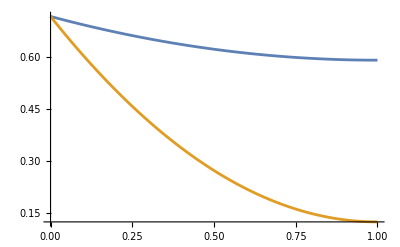

```mathematica
(*Plot[{Rdiff/.subS2W,dRdiff/.subS2W,σμplus/((2 GF^2 Me Enu)/π)},{y,0,1}]//Simplify*)
Plot[{σμplus/((2 GF^2 Me Enu)/π)/.subG/.subS2W,σμminus/((2 GF^2 Me Enu)/π)/.subG/.subS2W},{y,0,1}]//Simplify
```

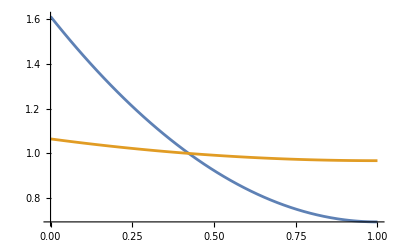

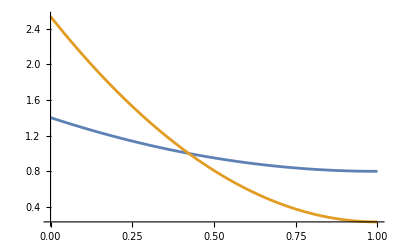

```mathematica
Plot[{(σν̄μ)/(σtotν̄μ)/.subG/.subS2W,σνe/σtotνe/.subG/.subS2W},{y,0,1}]//Simplify
Plot[{σνμ/σtotνμ/.subG/.subS2W,(σν̄e)/(σtotν̄e)/.subG/.subS2W},{y,0,1}]//Simplify
```

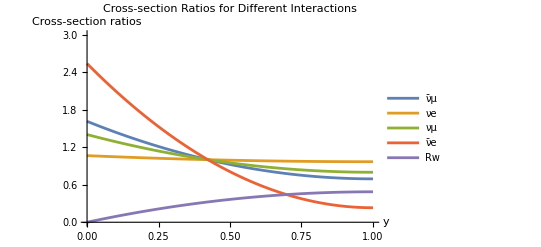

```mathematica
(*First Plot with Legends and Labels*)Plot[{σν̄μ/σtotν̄μ/. subG/. subS2W,σνe/σtotνe/. subG/. subS2W,σνμ/σtotνμ/. subG/. subS2W,σν̄e/σtotν̄e/. subG/. subS2W,Rdiff/. subG/. subS2W},{y,0,1},PlotLegends->{"ν̄μ","νe","νμ","ν̄e","Rw"},AxesLabel->{"y","Cross-section ratios"},PlotLabel->"Cross-section Ratios for Different Interactions",LabelStyle->Directive[Bold],PlotRange->{{0,1},{0,3}}]//Simplify
```

```mathematica
(σtotνe+σtotν̄μ)/. subG//FullSimplify
(σtotνμ+σtotν̄e)/. subG//FullSimplify
```

(2 Enu GF^2 Me (1+2 s2W+8 s2W^2))/(3 π)

(2 Enu GF^2 Me (1-2 s2W+8 s2W^2))/(3 π)

```mathematica
""
```

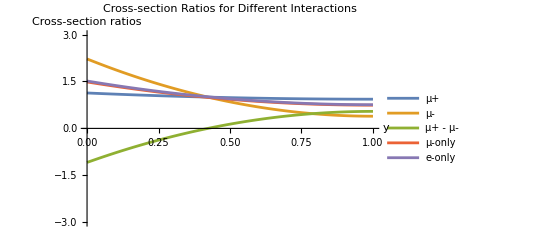

```mathematica
Plot[{(σν̄μ+σνe)/(σtotνe+σtotν̄μ)/. subG/. subS2W,(σνμ+σν̄e)/(σtotνμ+σtotν̄e)/. subG/. subS2W,(σν̄μ+σνe)/(σtotνe+σtotν̄μ)-(σνμ+σν̄e)/(σtotνμ+σtotν̄e)/. subG/. subS2W, 0.99*(σν̄μ+σνμ)/(σtotνμ+σtotν̄μ)/. subG/. subS2W,1.01(σνe+σν̄e)/(σtotνe+σtotν̄e)/. subG/. subS2W},{y,0,1},PlotLegends->{"µ+","µ-","µ+ - µ-","µ-only","e-only"},AxesLabel->{"y","Cross-section ratios"},PlotLabel->"Cross-section Ratios for Different Interactions",LabelStyle->Directive[Bold],PlotRange->{{0,1},{-3,3}}]//Simplify
```

```mathematica
σμplus/((2 GF^2 Me Enu)/π)
```

1+2 gL+gL^2 (2-2 y+y^2)+gR^2 (2-2 y+y^2)

```mathematica
(σμplus - σμminus)/((2 GF^2 Me Enu)/π)/.y-> Ee/Enu/.subG//FullSimplify
(σμplus - σμminus)/(σμplus + σμminus)/.y-> 1 -(ET2/(2 Me))/.subG//FullSimplify
y(-2+y)/.y-> 1 -(ET2/(2 Me))/.subG//FullSimplify
```

-(2 Ee (Ee-2 Enu) s2W)/Enu^2

-(4 (ET2^2-4 Me^2) s2W)/((ET2^2+4 Me^2) (1+8 s2W^2))

-1+ET2^2/(4 Me^2)

```mathematica
Rdiff/.subS2W/.y-> 1
```

0.486845